```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
```

## MMC

```mathematica
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc\\O-O2-Pt"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc\O-O2-Pt

```mathematica
{TogglerBar[Dynamic[cfiles],FileNames["*.confs"],Appearance->"Vertical"],TogglerBar[Dynamic[efiles],FileNames["*.en"],Appearance->"Vertical"],TogglerBar[Dynamic[hfiles],FileNames["*.hist"],Appearance->"Vertical"]}
```

{,,TogglerBar[,{},Appearance→Vertical]}

```mathematica
data=Import[#,"Table"]&/@cfiles;
{nrows,ncols,Tstep}=data[[All,2]]ᵀ;
snames=data[[All,3]];
nsteps=Position [Flatten[#,0],"step"][[All,1]]&/@data;
nads=Table[data[[ifile,nsteps[[ifile,i]]+1]],{ifile,Length[data]},{i,Length[nsteps[[ifile]]]}];
adslist=Table[data[[ifile,nsteps[[ifile,i]]+2;;nsteps[[ifile,i]]+2+Total[nads[[ifile,i]]]-1]],{ifile,Length[data]},{i,Length[nsteps[[ifile]]]}];
occs=Table[Normal[SparseArray[adslist[[ifile,i,All,{2,3}]]->adslist[[ifile,i,All,1]],{nrows[[ifile]],ncols[[ifile]]}]],{ifile,Length[data]},{i,Length[nsteps[[ifile]]]}];
data = .
```

```mathematica
energy=Import[#,"Table"]&/@efiles;
```

```mathematica
data=Import[#,"Table"]&/@hfiles;
hrefs=Position[#,"counts"][[All,1]]&/@data;
nspecies=Table[(Differences[Append[hrefs[[ifile]],Length[data[[ifile]]]+1]]-1)/2,{ifile,Length[data]}];
hist=Table[data[[ifile,hrefs[[ifile,i]]+2species]],{ifile,Length[data]},{i,Length[hrefs[[ifile]]]},{species,nspecies[[ifile,i]]}];
(* hist[ file, record, species, number of clusters ] *)
data=.
```

```mathematica
energy
```

{{{0,Infinity},{100,Infinity},{200,Infinity},{300,Infinity},{400,Infinity},{500,Infinity},{600,Infinity},{700,Infinity},{800,Infinity},{900,Infinity},{1000,Infinity},{1100,Infinity},{1200,Infinity},{1300,Infinity},{1400,Infinity},{1500,Infinity},{1600,Infinity},{1700,Infinity},{1800,Infinity},{1900,Infinity},{2000,Infinity},{2100,Infinity},{2200,Infinity},{2300,Infinity},{2400,Infinity},{2500,Infinity},{2600,Infinity},{2700,Infinity},{2800,Infinity},{2900,Infinity},{3000,Infinity},{3100,Infinity},{3200,Infinity},{3300,Infinity},{3400,Infinity},{3500,Infinity},{3600,Infinity},{3700,Infinity},{3800,Infinity},{3900,Infinity},{4000,Infinity},{4100,Infinity},{4200,Infinity},{4300,Infinity},{4400,Infinity},{4500,Infinity},{4600,Infinity},{4700,Infinity},{4800,Infinity},{4900,Infinity},{5000,Infinity},{5100,Infinity},{5200,Infinity},{5300,Infinity},{5400,Infinity},{5500,Infinity},{5600,Infinity},{5700,Infinity},{5800,Infinity},{5900,Infinity},{6000,Infinity},{6100,Infinity},{6200,Infinity},{6300,Infinity},{6400,Infinity},{6500,Infinity},{6600,Infinity},{6700,Infinity},{6800,Infinity},{6900,Infinity},{7000,Infinity},{7100,Infinity},{7200,Infinity},{7300,Infinity},{7400,Infinity},{7500,Infinity},{7600,Infinity},{7700,Infinity},{7800,Infinity},{7900,Infinity},{8000,Infinity},{8100,Infinity},{8200,Infinity},{8300,Infinity},{8400,Infinity},{8500,Infinity},{8600,Infinity},{8700,Infinity},{8800,Infinity},{8900,Infinity},{9000,Infinity},{9100,Infinity},{9200,Infinity},{9300,Infinity},{9400,Infinity},{9500,Infinity},{9600,Infinity},{9700,Infinity},{9800,Infinity},{9900,Infinity},{10000,Infinity}}}

```mathematica
ListLinePlot[energy,PlotRange->All,FrameLabel->{"MMC steps","Energy (meV)"},ImageSize->Large]
```

-Graphics-

```mathematica
size=Range[1,Length[#[[-1]]]]&/@hist;
```

```mathematica
(size[[1]] hist[[1,-1]])/nhsteps[[-1]]
```

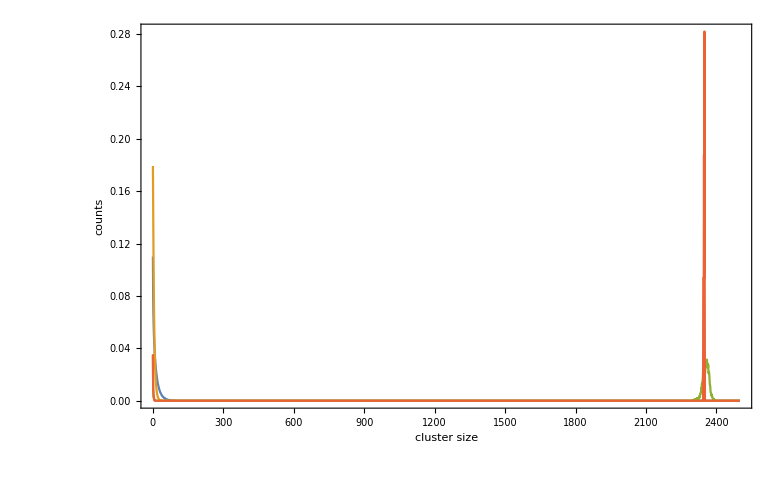

```mathematica
ListLinePlot[{(size hist[[-1]])/(nhsteps[[-1]]nads2),(size hist3[[-1]])/(nhsteps3[[-1]]nads3),(size hist5[[-1]])/(nhsteps5[[-1]]nads5),(size hist5[[1]])/(nhsteps5[[1]]nads5)},FrameLabel->{"cluster size","counts"},PlotRange->{All,All}]
```

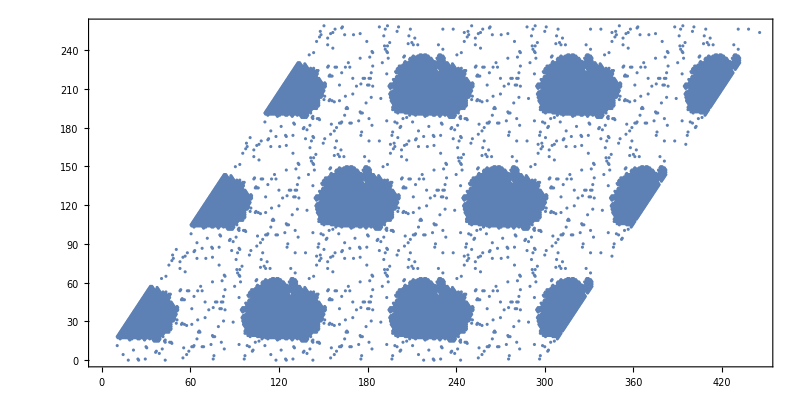

```mathematica
ListPlot[(((#-{1,1})&/@Position[ArrayPad[occs5[[-1]],nlat,"Periodic"],1]).{{1,0},{Cos[π/3],Sin[π/3]}}),AspectRatio->Cos[π/3]]
```

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs5[[i]],nlat,"Periodic"],ColorFunction->"Monochrome"],{i,1,nframes,1}]
```

Part::partd: Part specification occs5⟦1⟧ is longer than depth of object.

ArrayPad::arr: First argument occs5⟦1⟧ to ArrayPad should be an array.

MatrixPlot::mat0: Argument occs5⟦1⟧ at position 1 is not a matrix.

Part::partd: Part specification occs5⟦1⟧ is longer than depth of object.

ArrayPad::arr: First argument occs5⟦1⟧ to ArrayPad should be an array.

MatrixPlot::mat0: Argument occs5⟦1⟧ at position 1 is not a matrix.

Part::partd: Part specification occs5⟦1⟧ is longer than depth of object.

ArrayPad::arr: First argument occs5⟦1⟧ to ArrayPad should be an array.

MatrixPlot::mat0: Argument occs5⟦1⟧ at position 1 is not a matrix.

Part::partd: Part specification occs5⟦1⟧ is longer than depth of object.

ArrayPad::arr: First argument occs5⟦1⟧ to ArrayPad should be an array.

MatrixPlot::mat0: Argument occs5⟦1⟧ at position 1 is not a matrix.

Part::partd: Part specification occs5⟦1⟧ is longer than depth of object.

ArrayPad::arr: First argument occs5⟦1⟧ to ArrayPad should be an array.

MatrixPlot::mat0: Argument occs5⟦1⟧ at position 1 is not a matrix.

Part::partd: Part specification occs5⟦1⟧ is longer than depth of object.

ArrayPad::arr: First argument occs5⟦1⟧ to ArrayPad should be an array.

MatrixPlot::mat0: Argument occs5⟦1⟧ at position 1 is not a matrix.

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs3[[i]],0,"Periodic"],ColorFunction->"Monochrome"],{i,1,nframes,1}]
```

## KMC

```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data

```mathematica
FileNames["*.csz"]
```

{kmc000001.csz}

```mathematica
energy=Import[#,"Table"]&/@FileNames["*.en"];
```

```mathematica
iemin=Ordering[energy[[1,All,2]]][[1]]
```

642

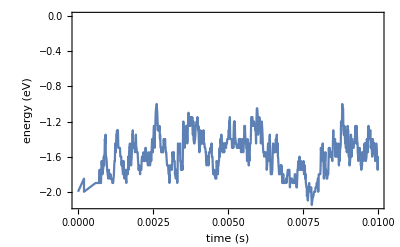

```mathematica
ListLinePlot[{energy[[1,All,1]],energy[[1,All,2]]}ᵀ,FrameLabel->{"time (s)","energy (eV)"}]
```

```mathematica
data=Import[#,"Table"]&/@FileNames["*.csz"];
{tend,nbins}=data[[1,1]];
time=tend/nbins Flatten[#]&/@data[[All,2;;;;2]];
csized=data[[All,3;;;;2]];
csizedm=Mean[csized];
```

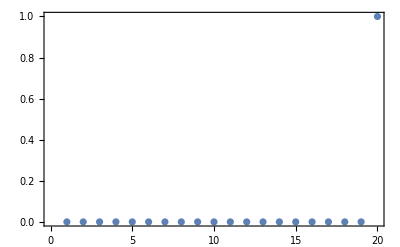

```mathematica
ListPlot[csizedm[[iemin]],PlotRange->Automatic]
```

```mathematica
Manipulate[ListPlot[csizedm[[i]],PlotRange->{{0,100},{0,2}}],{i,1,nbins,1}]
```

## Compare MMC and KMC

### nlat020T1000c0250

```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc_vs_kmc\\nlat020T1000c0250"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc_vs_kmc\nlat020T1000c0250

```mathematica
cfiles=FileNames["mmc*.confs"];
efiles=FileNames["mmc*.en"]
hfiles=FileNames["mmc*.hist"];
```

{mmc.en,mmc_eq.en,mmc_eq_i005.en,mmc_i005.en,mmc_melt.en,mmc_melt_i005.en}

```mathematica
kmcefiles=FileNames["kmc*.en"];
kmchfiles=FileNames["kmc*.csz"];
```

```mathematica
data=Import[#,"Table"]&/@cfiles;
{nlat,nads}=data[[All,1]]ᵀ
occs=Table[Partition[data[[i,2;;]],nlat[[i]]],{i,Length[data]}];
nframes=Length/@occs

energy=Import[#,"Table"]&/@efiles;
kmcenergy=Import[#,"Table"]&/@kmcefiles;
```

{{20,20,20,20,20,20},{100,100,100,100,100,100}}

{1001,101,101,1001,101,101}

```mathematica
data=Import[#,"Table"]&/@hfiles;
nhsteps=Flatten[data[[All,;;;;2]],{{3},{1,2}}];
hist=data[[All,2;;;;2]];
data=.
```

```mathematica
data=Import[#,"Table"]&/@kmchfiles;
```

```mathematica
tend=data[[1,1,1]]
kmcnhist=data[[1,1,2]]-1
```

0.01

999

```mathematica
ibin=Flatten[data[[All,2;;;;2]]];
kmchist=data[[All,3;;;;2]];
```

```mathematica
kmcenplot=ListLinePlot[{kmcenergy[[1,All,1]] 100000/0.01,kmcenergy[[1,All,2]]}ᵀ,PlotRange->All,FrameLabel->{"time (s)","Energy (meV)"},ImageSize->Large,PlotStyle->Red];
```

```mathematica
{Mean[energy[[-1,All,2]]],Variance[energy[[-1,All,2]]]}
{Mean[kmcenergy[[1,All,2]]],Variance[kmcenergy[[1,All,2]]]}
```

{-8.52703,3.54062}

{-0.92454,0.0483257}

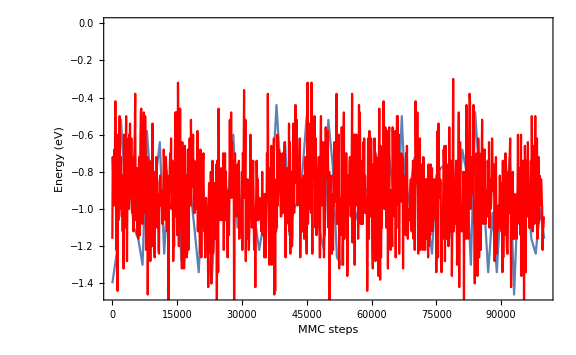

```mathematica
Show[ListLinePlot[energy[[2]],PlotRange->All,FrameLabel->{"MMC steps","Energy (eV)"},ImageSize->Large],kmcenplot]
```

```mathematica
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[1,i]],0nlat[[1]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-1,1 1.5nlat[[1]]},{-1,1nlat[[1]]}},PlotMarkers->{Automatic,22},Frame->None,ImageSize->Large],{i,1,nframes[[1]],1}]
```

```mathematica
itr=-1;
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[itr,i]],nlat[[itr]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-3,3 1.5nlat[[itr]]},{-3,3nlat[[itr]]}},PlotMarkers->{Automatic,10},Frame->None,ImageSize->Large],{i,1,nframes[[itr]],1}]
```

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs[[1,i]],nlat[[1]],"Periodic"],ColorFunction->"Monochrome",Mesh->All,MeshStyle->Directive[LightGray]],{i,1,nframes[[1]],1}]
```

```mathematica
nhsteps[[1,-1]]
```

1000

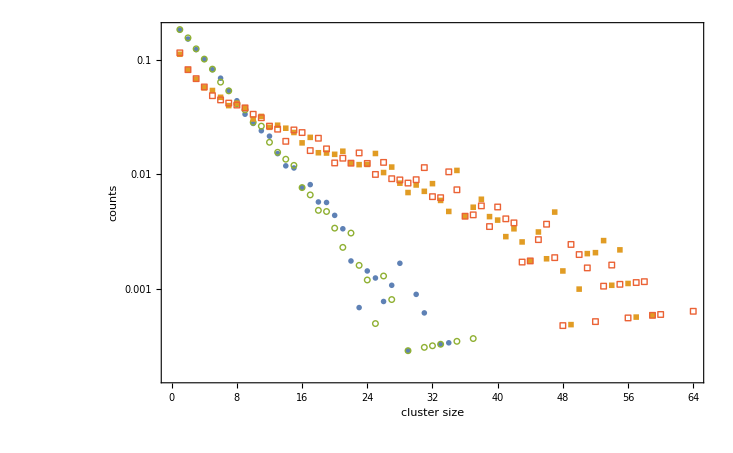

```mathematica
size=Range[1,Length[#[[-1]]]]&/@hist;
cp1000=ListLogPlot[{(size[[1]] hist[[1,-1]])/(nhsteps[[1,-1]]nads[[1]]),(size[[2]] hist[[2,-1]])/(nhsteps[[1,-1]]nads[[1]]),(size[[1]]Mean[kmchist[[1]]])/nads[[1]],(size[[2]]Mean[kmchist[[2]]])/nads[[2]]},FrameLabel->{"cluster size","counts"},PlotRange->{All,All},PlotMarkers->{{●, 8},{■, 8}, {○, 8}, {□, 8}}]
```

### nlat020T0600c0250

```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc_vs_kmc\\nlat020T0600c0250"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc_vs_kmc\nlat020T0600c0250

```mathematica
cfiles=FileNames["mmc*.confs"];
efiles=FileNames["mmc*.en"]
hfiles=FileNames["mmc*.hist"];
```

{mmc.en,mmc_eq.en}

```mathematica
kmcefiles=FileNames["kmc*.en"];
kmchfiles=FileNames["kmc*.csz"];
```

```mathematica
data=Import[#,"Table"]&/@cfiles;
{nlat,nads}=data[[All,1]]ᵀ
occs=Table[Partition[data[[i,2;;]],nlat[[i]]],{i,Length[data]}];
nframes=Length/@occs

energy=Import[#,"Table"]&/@efiles;
```

{{20,20},{100,100}}

{1001,101}

```mathematica
kmcenergy=Import[#,"Table"]&/@kmcefiles;
```

```mathematica
data=Import[#,"Table"]&/@hfiles;
nhsteps=Flatten[data[[All,;;;;2]],{{3},{1,2}}];
hist=data[[All,2;;;;2]];
data=.
```

```mathematica
data=Import[#,"Table"]&/@kmchfiles;
```

```mathematica
tend=data[[1,1,1]]
kmcnhist=data[[1,1,2]]-1
```

0.01

999

```mathematica
ibin=Flatten[data[[1,2;;;;2]]];
kmchist=data[[1,3;;;;2]];
```

```mathematica
kmcenplot=ListLinePlot[{kmcenergy[[1,All,1]] 100000/0.01,kmcenergy[[1,All,2]]}ᵀ,PlotRange->All,FrameLabel->{"time (s)","Energy (meV)"},ImageSize->Large,PlotStyle->Red];
```

```mathematica
{Mean[energy[[1,All,2]]],Variance[energy[[1,All,2]]]}
{Mean[kmcenergy[[1,All,2]]],Variance[kmcenergy[[1,All,2]]]}
```

{-1.27716,0.0450927}

Part::partd: Part specification kmcefiles⟦1,All,2⟧ is longer than depth of object.

{Mean[kmcefiles⟦1,All,2⟧],Variance[kmcefiles⟦1,All,2⟧]}

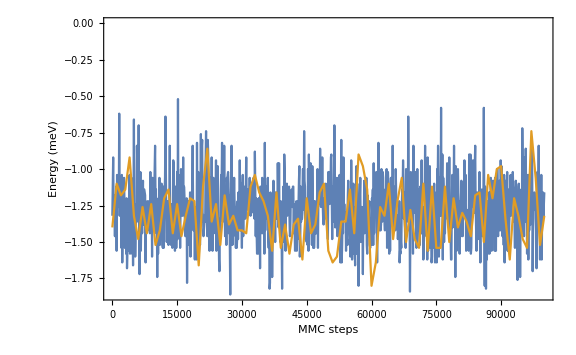

```mathematica
energyplot=ListLinePlot[energy,PlotRange->All,FrameLabel->{"MMC steps","Energy (meV)"},ImageSize->Large]
```

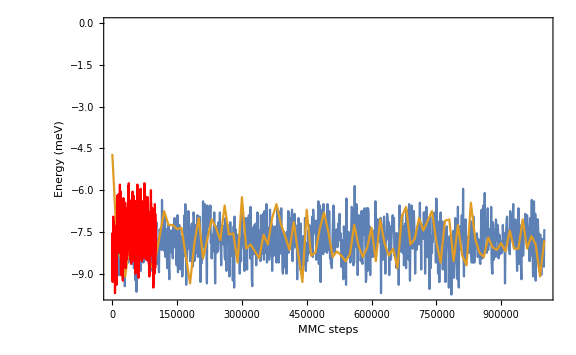

```mathematica
Show[energyplot,kmcenplot]
```

```mathematica
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[1,i]],0nlat[[1]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-1, 1.5nlat[[1]]},{-1,nlat[[1]]}},PlotMarkers->{Automatic,22},Frame->None,ImageSize->Large],{i,1,nframes[[1]],1}]
```

```mathematica
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[1,i]],nlat[[1]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-3,3 1.5nlat[[1]]},{-3,3nlat[[1]]}},PlotMarkers->{Automatic,10},Frame->None,ImageSize->Large],{i,1,nframes[[1]],1}]
```

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs[[1,i]],nlat[[1]],"Periodic"],ColorFunction->"Monochrome",Mesh->All,MeshStyle->Directive[LightGray]],{i,1,nframes[[1]],1}]
```

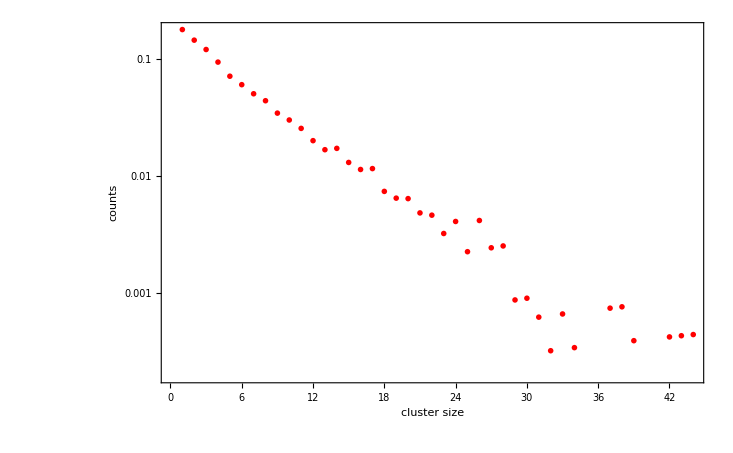

```mathematica
size=Range[1,Length[#[[-1]]]]&/@hist;
cp600=ListLogPlot[{(size[[1]] hist[[1,-1]])/(nhsteps[[1,-1]]nads[[1]])(*,(size[[1]]Mean[kmchist])/nads[[1]]*)},FrameLabel->{"cluster size","counts"},PlotRange->{All,All},PlotMarkers->{{●, 8}, {○, 8}},PlotStyle->Red]
```

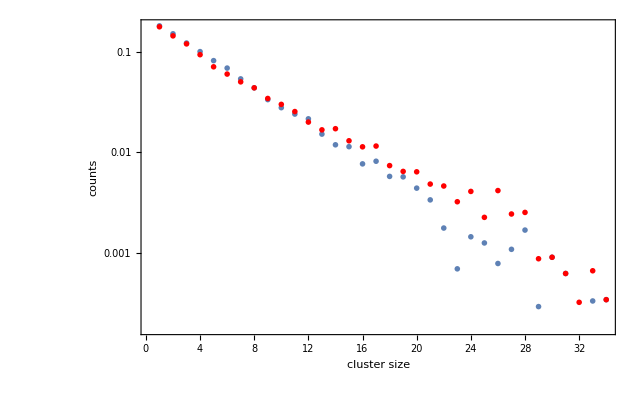

```mathematica
Show[cp1000,cp600]
```

## Compare MMC and KMC V0.1

### nlat020T1000c0250

```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc_vs_kmc"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc_vs_kmc

```mathematica
cfiles=FileNames["mmc*.confs"];
efiles=FileNames["mmc*.en"]
hfiles=FileNames["mmc*.hist"];
```

{mmc.en,mmc_eq.en,mmc_melt.en}

```mathematica
kmcefiles=FileNames["kmc*.en"];
kmchfiles=FileNames["kmc*.csz"];
```

```mathematica
data=Import[#,"Table"]&/@cfiles;
{nlat,nads}=data[[All,1]]ᵀ
occs=Table[Partition[data[[i,2;;]],nlat[[i]]],{i,Length[data]}];
nframes=Length/@occs

energy=Import[#,"Table"]&/@efiles;
kmcenergy=Import[#,"Table"]&/@kmcefiles;
```

{{20,20,20},{100,100,100}}

{1001,101,101}

```mathematica
data=Import[#,"Table"]&/@hfiles;
nhsteps=Flatten[data[[All,;;;;2]],{{3},{1,2}}];
hist=data[[All,2;;;;2]];
data=.
```

```mathematica
data=Import[#,"Table"]&/@kmchfiles;
```

```mathematica
tend=data[[1,1,1]]
kmcnhist=data[[1,1,2]]-1
```

0.01

999

```mathematica
ibin=Flatten[data[[1,2;;;;2]]];
kmchist=data[[1,3;;;;2]];
```

```mathematica
kmcenplot=ListLinePlot[{kmcenergy[[1,All,1]] 100000/0.01,kmcenergy[[1,All,2]]}ᵀ,PlotRange->All,FrameLabel->{"time (s)","Energy (meV)"},ImageSize->Large,PlotStyle->Red];
```

```mathematica
{Mean[energy[[1,All,2]]],Variance[energy[[1,All,2]]]}
{Mean[kmcenergy[[1,All,2]]],Variance[kmcenergy[[1,All,2]]]}
```

{-5.42707,0.213671}

{-5.38195,0.222709}

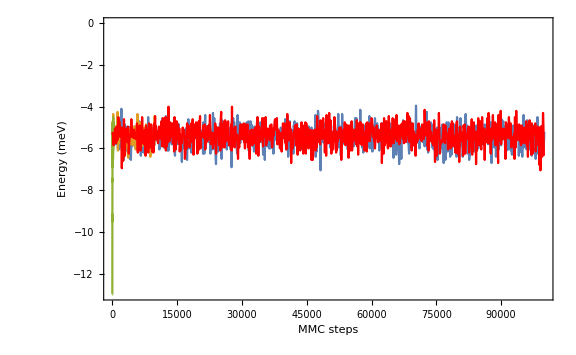

```mathematica
Show[ListLinePlot[energy,PlotRange->All,FrameLabel->{"MMC steps","Energy (meV)"},ImageSize->Large],kmcenplot]
```

```mathematica
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[1,i]],0nlat[[1]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-1,1 1.5nlat[[1]]},{-1,1nlat[[1]]}},PlotMarkers->{Automatic,22},Frame->None,ImageSize->Large],{i,1,nframes[[1]],1}]
```

```mathematica
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[1,i]],nlat[[1]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-3,3 1.5nlat[[1]]},{-3,3nlat[[1]]}},PlotMarkers->{Automatic,10},Frame->None,ImageSize->Large],{i,1,nframes[[1]],1}]
```

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs[[1,i]],nlat[[1]],"Periodic"],ColorFunction->"Monochrome",Mesh->All,MeshStyle->Directive[LightGray]],{i,1,nframes[[1]],1}]
```

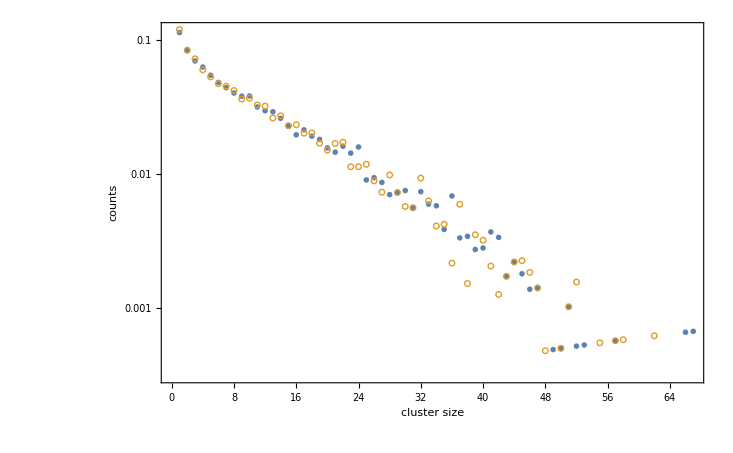

```mathematica
size=Range[1,Length[#[[-1]]]]&/@hist;
ListLogPlot[{(size[[1]] hist[[1,-1]])/(nhsteps[[1,-1]]nads[[1]]),(size[[1]]Mean[kmchist])/nads[[1]]},FrameLabel->{"cluster size","counts"},PlotRange->{All,All},PlotMarkers->{{●, 8}, {○, 8}}]
```

### nlat020T0600c0250

```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc_vs_kmc"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc_vs_kmc

```mathematica
cfiles=FileNames["mmc*.confs"];
efiles=FileNames["mmc*.en"]
hfiles=FileNames["mmc*.hist"];
```

{mmc.en,mmc_eq.en}

```mathematica
kmcefiles=FileNames["kmc*.en"];
kmchfiles=FileNames["kmc*.csz"];
```

```mathematica
data=Import[#,"Table"]&/@cfiles;
{nlat,nads}=data[[All,1]]ᵀ
occs=Table[Partition[data[[i,2;;]],nlat[[i]]],{i,Length[data]}];
nframes=Length/@occs

energy=Import[#,"Table"]&/@efiles;
```

{{20,20},{100,100}}

{1001,101}

```mathematica
kmcenergy=Import[#,"Table"]&/@kmcefiles;
```

```mathematica
data=Import[#,"Table"]&/@hfiles;
nhsteps=Flatten[data[[All,;;;;2]],{{3},{1,2}}];
hist=data[[All,2;;;;2]];
data=.
```

```mathematica
data=Import[#,"Table"]&/@kmchfiles;
```

```mathematica
tend=data[[1,1,1]]
kmcnhist=data[[1,1,2]]-1
```

0.01

999

```mathematica
ibin=Flatten[data[[1,2;;;;2]]];
kmchist=data[[1,3;;;;2]];
```

```mathematica
kmcenplot=ListLinePlot[{kmcenergy[[1,All,1]] 100000/0.01,kmcenergy[[1,All,2]]}ᵀ,PlotRange->All,FrameLabel->{"time (s)","Energy (meV)"},ImageSize->Large,PlotStyle->Red];
```

```mathematica
{Mean[energy[[1,All,2]]],Variance[energy[[1,All,2]]]}
{Mean[kmcenergy[[1,All,2]]],Variance[kmcenergy[[1,All,2]]]}
```

{-7.80659,0.454796}

{-7.58885,0.455564}

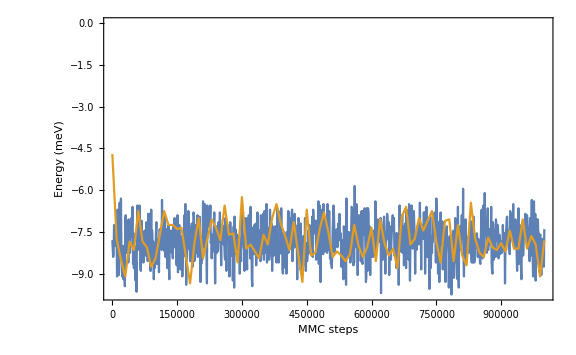

```mathematica
energyplot=ListLinePlot[energy,PlotRange->All,FrameLabel->{"MMC steps","Energy (meV)"},ImageSize->Large]
```

```mathematica
Show[energyplot,kmcenplot]
```

-Graphics-

```mathematica
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[1,i]],0nlat[[1]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-1, 1.5nlat[[1]]},{-1,nlat[[1]]}},PlotMarkers->{Automatic,22},Frame->None,ImageSize->Large],{i,1,nframes[[1]],1}]
```

```mathematica
Manipulate[ListPlot[((#-{1,1})&/@Position[ArrayPad[occs[[1,i]],nlat[[1]],"Periodic"],_?Positive]).{{1,0},{Cos[π/3],Sin[π/3]}},PlotRange->{{-3,3 1.5nlat[[1]]},{-3,3nlat[[1]]}},PlotMarkers->{Automatic,10},Frame->None,ImageSize->Large],{i,1,nframes[[1]],1}]
```

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs[[1,i]],nlat[[1]],"Periodic"],ColorFunction->"Monochrome",Mesh->All,MeshStyle->Directive[LightGray]],{i,1,nframes[[1]],1}]
```

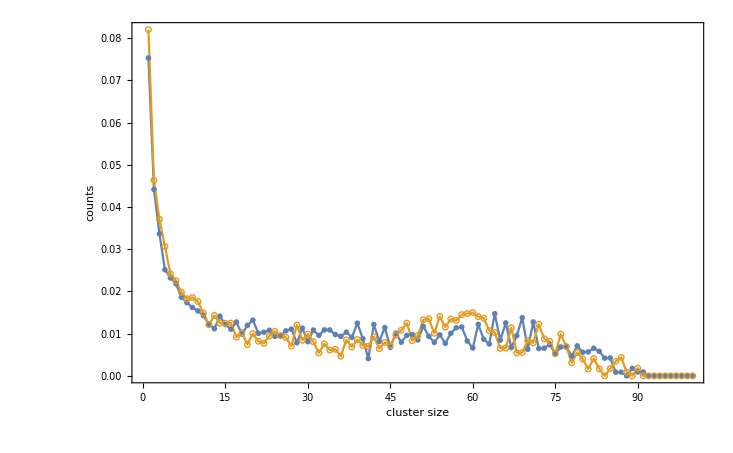

```mathematica
size=Range[1,Length[#[[-1]]]]&/@hist;
ListLinePlot[{(size[[1]] hist[[1,-1]])/(nhsteps[[1,-1]]nads[[1]]),(size[[1]]Mean[kmchist])/nads[[1]]},FrameLabel->{"cluster size","counts"},PlotRange->{All,All},PlotMarkers->{{●, 8}, {○, 8}}]
```